## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
```

```mathematica
(*Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]*)
```

```mathematica
<<"/home/strelda/Documents/programování/Mathematica/packages/GRQUICK/GRQUICKv4.m"
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-5/2-λ/4 | -χ/(2 √5) | -λ/(√10) | 0 | 0 | 0
-χ/(2 √5) | 1/20 (-30-13 λ-4 χ^2) | -(3 √2 χ)/5 | -(3 λ)/(5 √2) | 0 | 0
-λ/(√10) | -(3 √2 χ)/5 | 1/20 (-17 λ-2 (5+8 χ^2)) | -(3 χ)/2 | -(3 λ)/(5 √2) | 0
0 | -(3 λ)/(5 √2) | -(3 χ)/2 | 1/20 (10-17 λ-36 χ^2) | -(7 √2 χ)/5 | -λ/(√10)
0 | 0 | -(3 λ)/(5 √2) | -(7 √2 χ)/5 | 1/20 (30-13 λ-64 χ^2) | -(9 χ)/(2 √5)
0 | 0 | 0 | -λ/(√10) | -(9 χ)/(2 √5) | 5/2-λ/4-5 χ^2)

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies

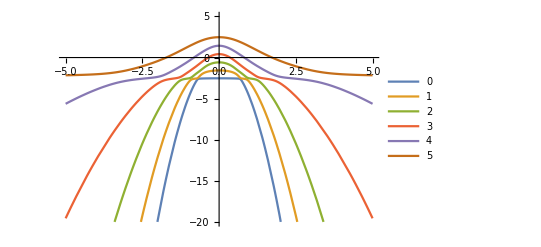

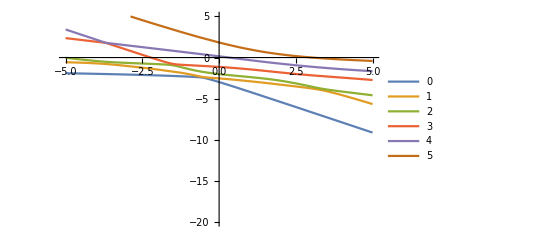

```mathematica
energies1=Eigenvalues[H[0.1,χ]];
energies2=Eigenvalues[H[λ,0.78]];
Plot[energies1,{χ,-5,5},PlotLegends->Range[0,10],PlotPoints->15,PlotRange->{Automatic,{-20,5}}]
Plot[energies2,{λ,-5,5},PlotLegends->Range[0,10],PlotPoints->5,PlotRange->{Automatic,{-20,5}}]
```

```mathematica
eigensys[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First]
]
eigensys1[λ_?NumericQ,χ_?NumericQ]:=
Sort@Eigenvalues[HC[λ,χ],Method->{"Banded"}
]
```

```mathematica
Plot3D[Query[1]@ND[eigensys1[λ,x],{x,2},χ]+Query[1]@ND[eigensys1[l,χ],{l,2},λ],{λ,-3,10},{χ,-1,1},ColorFunction->"SunsetColors",PlotPoints->150,ExclusionsStyle->{None, Red},Exclusions->Automatic,ClippingStyle->None,PerformanceGoal->"Quality"]
```

-Graphics3D-

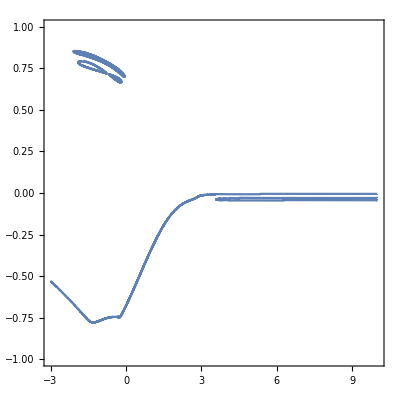

```mathematica
ContourPlot[1/(Query[1]@ND[eigensys1[λ,x],{x,1},χ]+Query[1]@ND[eigensys1[l,χ],{l,1},λ])==0,{λ,-3,10},{χ,-1,1},PlotPoints->200,PerformanceGoal->"Quality"]
```

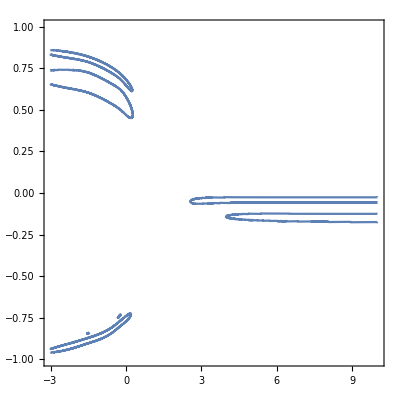

```mathematica
ContourPlot[1/(Query[1]@ND[eigensys1[λ,x],{x,2},χ]+Query[1]@ND[eigensys1[l,χ],{l,2},λ])==0,{λ,-3,10},{χ,-1,1},PlotPoints->200,PerformanceGoal->"Quality"]
```

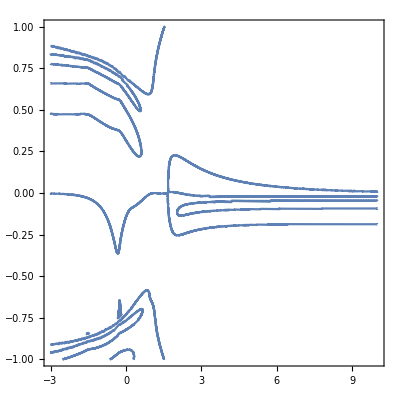

```mathematica
ContourPlot[1/(Query[1]@ND[eigensys1[λ,x],{x,3},χ]+Query[1]@ND[eigensys1[l,χ],{l,3},λ])==0,{λ,-3,10},{χ,-1,1},PlotPoints->200,PerformanceGoal->"Quality"]
```

```mathematica
bge0e1=DensityPlot[Det[gC[l,x]],{l,-3,10},{x,-1,1},Evaluate@densityPlotOptions,PlotPoints->30,ScalingFunctions->"Log10",PlotRange->Full];
```

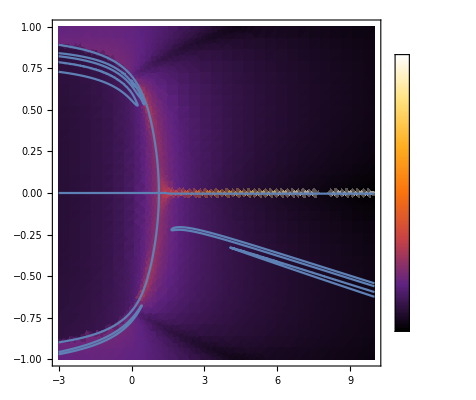

```mathematica
e0e1=ContourPlot[Query[1]@ND[eigensys1[λ,x],x,χ]-Query[2]@ND[eigensys1[λ,x],x,χ]==0,{λ,-3,10},{χ,-1,1},PlotPoints->100,PerformanceGoal->"Quality"];
Show[bge0e1,e0e1]
```

```mathematica
coord = Cases[Normal@e0e1,Line[x_]:>x,Infinity];
ListLinePlot[coord,PlotRange->{{-0.5,1.5},{-1,1}},Frame->True]
```

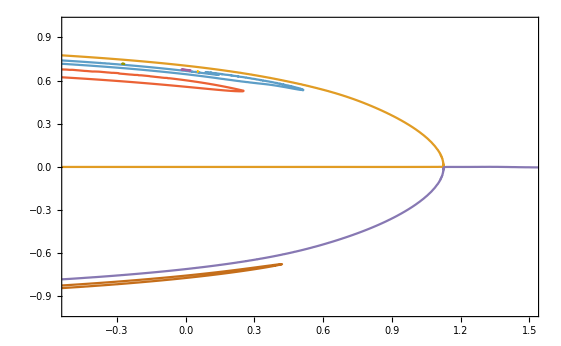

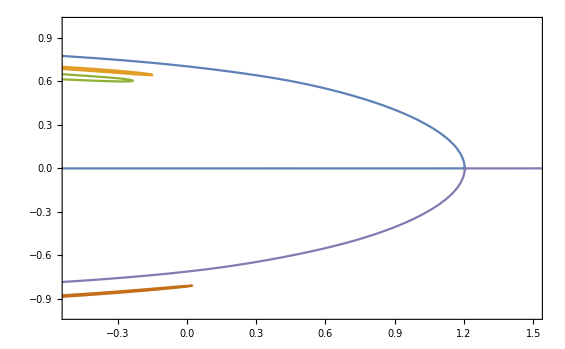

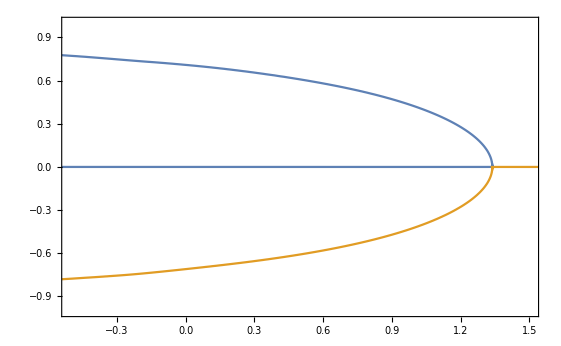

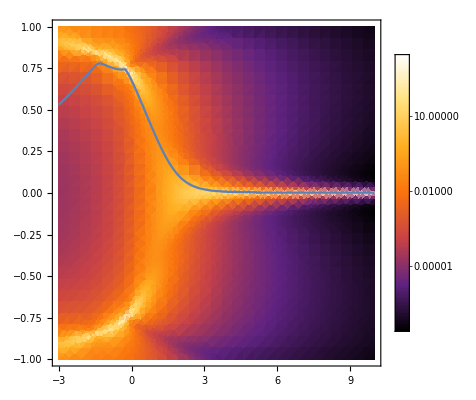

```mathematica
e0e0=ContourPlot[Query[1,1]@ND[eigensys[λ,x],x,χ,Terms->20]-Query[1,1]@ND[eigensys[l,χ],l,λ,Terms->20]==0,{λ,-3,10},{χ,-1,1},PlotPoints->70];
Show[bge0e1,e0e0]
```

## Metric tensor

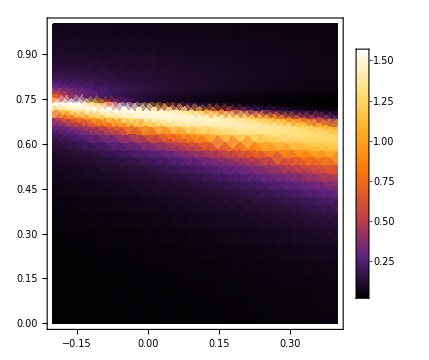
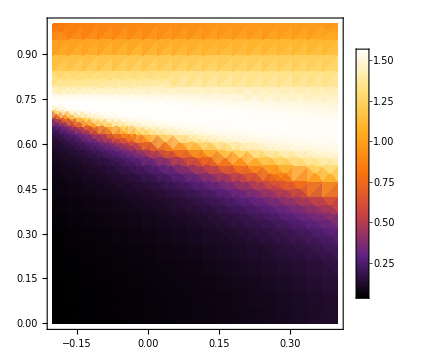
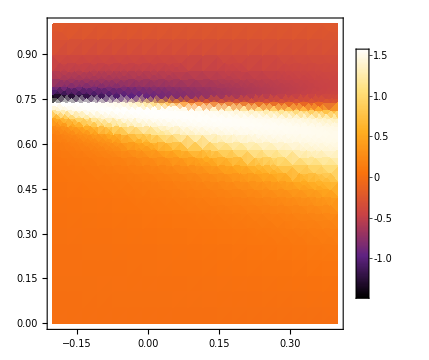

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
{DensityPlot[ArcTan[gC[y,x]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

#### Metric tensor determinant

```mathematica
DensityPlot[Det[gC[x,l]],{x,0,2.5},{l,0,2},Evaluate@densityPlotOptions,PlotPoints->300,ScalingFunctions->"Log10",PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[Det[gC[l,x]],{l,-0.5,2.5},{x,0,2},PlotPoints->50,Evaluate@font,ScalingFunctions->"Log10", ColorFunction->"SunsetColors",AxesLabel->MaTeX/@{"\\lambda","\\chi","Det(g)"}]
```

-Graphics3D-

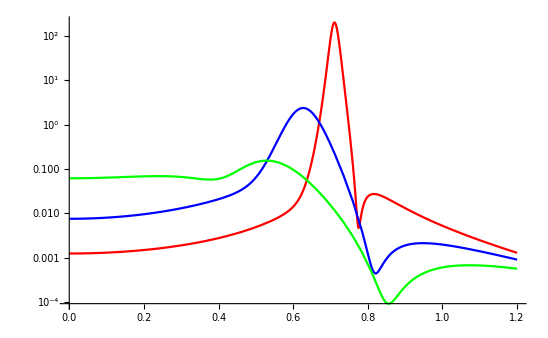

```mathematica
Plot[Evaluate[Det[gC[#,x]]&/@{0,0.5,1}],{x,0,1.2},PlotStyle->{Red,Blue,Green,Magenta,Purple},ScalingFunctions->"Log10"]
```

# Compiled geod function and Christoffel symbols

For huge matrices compute only first few energies and check for precission {vals,vecs}=Eigensystem[s,10]

Enable more functions to be compilable, for example Inverse

```mathematica
(*Internal`CompileValues[];(*to trigger auto-load*)ClearAttributes[Internal`CompileValues,ReadProtected];
syms=DownValues[Internal`CompileValues]/.HoldPattern[Verbatim[HoldPattern][Internal`CompileValues[sym_]]:>_]:>sym;
Complement[syms,Compile`CompilerFunctions[]]*)
```

## Define area for derivative precision

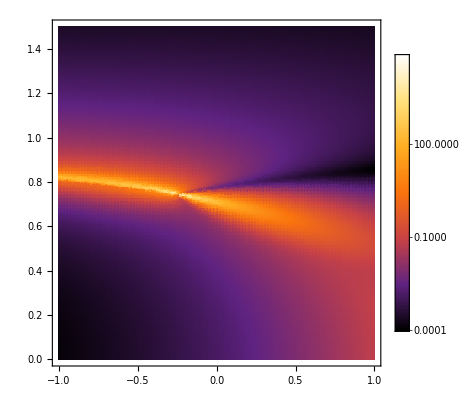

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1,1},{χ,0,1.5},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->100]
```

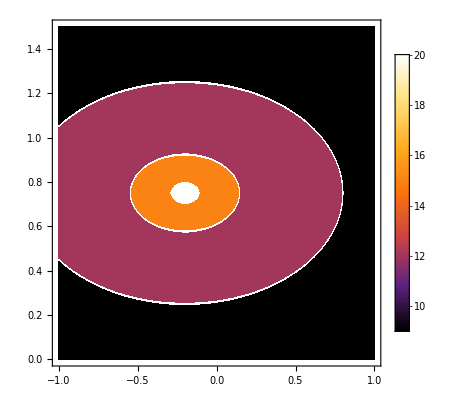

```mathematica
{c1,c2}={-0.2,0.75};
derPiece[λ_,χ_]:=Piecewise[{{20,(λ-c1)^2/4+(χ-c2)^2<0.002},{15,(λ-c1)^2/4+(χ-c2)^2<0.03},{12,(λ-c1)^2/4+(χ-c2)^2<0.25}},9]
circ=DensityPlot[derPiece[λ,χ],{λ,-1,1},{χ,0,1.5},Evaluate@densityPlotOptions]
```

## Defining compiled functions

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
(*G1[λ_?NumericQ,χ_?NumericQ]:=Module[{c,l,dg1,dg2,gInv1,gInv2},
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦1,#⟧&/@{1,2};
{gInv1 dg1⟦1,1⟧+gInv2(2dg1⟦1,2⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
];
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{c,l,dg1,dg2,gInv1,gInv2},
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦2,#⟧&/@{1,2};
{ gInv1 dg1⟦1,1⟧+ gInv2(dg1⟦1,2⟧+dg1⟦2,1⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
]*)
```

Check Christoffel symbols. If wrong, increase derTerms.

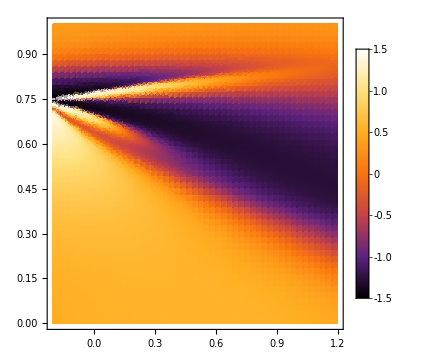
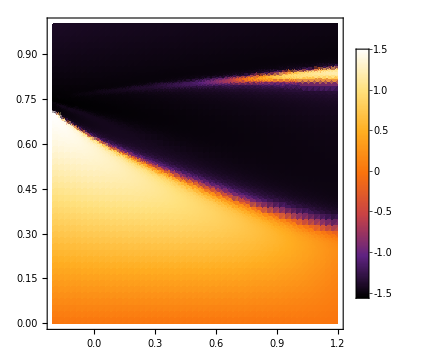
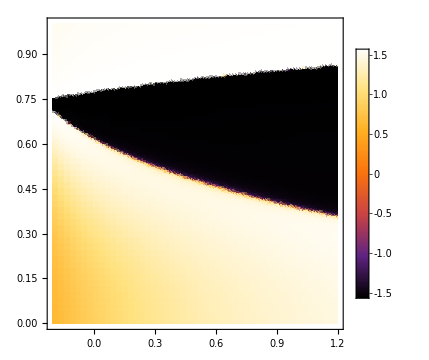

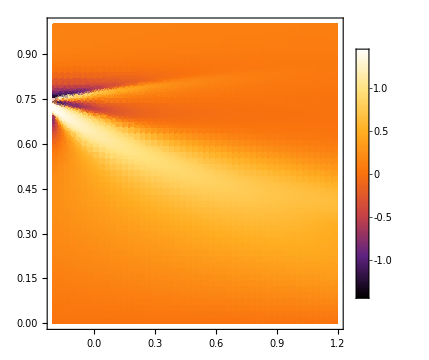
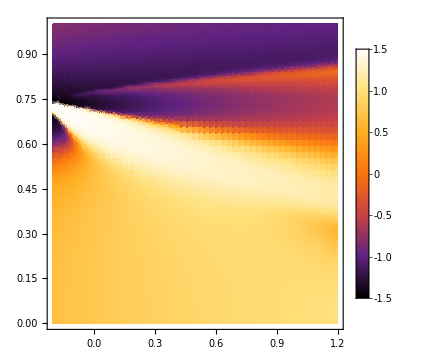
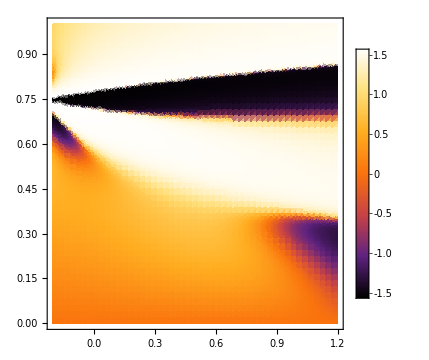

```mathematica
DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->50]&/@{1,2,3}
DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->50]&/@{1,2,3}
```

## Boundary value problem

```mathematica
tmax=10;
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
Timing@NDSolve[Join[eq,dirichlet[0,0,0,0.6]]
,{λ,χ},{t,0,tmax},
PrecisionGoal->2,AccuracyGoal->2]
```

{30.2044,{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
(*solP=ParametricNDSolve[Join[eq,dirichlet[0,0,0.3,f2]],{λ,χ},{t,0,tmax},{f2},PrecisionGoal->2,AccuracyGoal->2]
ParametricPlot[Evaluate@Table[{λ[f2][t],χ[f2][t]}/.solP,{f2,0,2,1}],{t,0,10},PlotRange->All]*)
```

```mathematica
solM=Quiet@Table[NDSolve[Join[eq,dirichlet[-1,i,1,i]],{λ,χ},{t,0,tmax},PrecisionGoal->3,AccuracyGoal->3],{i,0.5,1,0.1}]
```

```mathematica
solM1={{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}},{{λ->InterpolatingFunction[…],χ->InterpolatingFunction[…]}}};
```

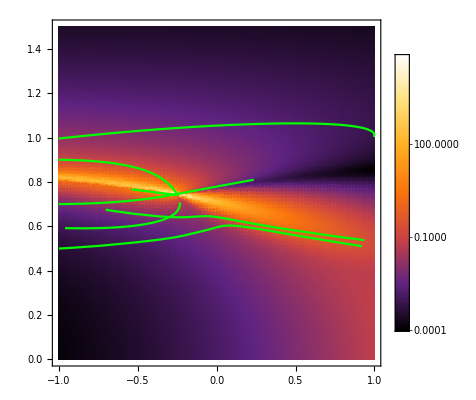

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

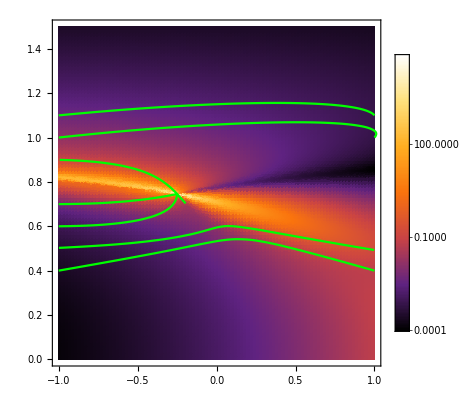

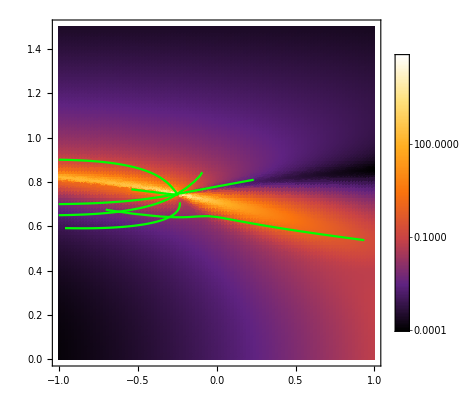

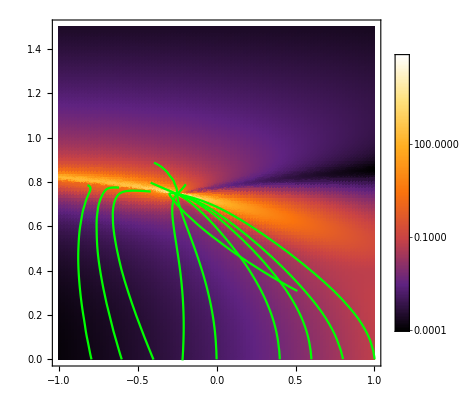

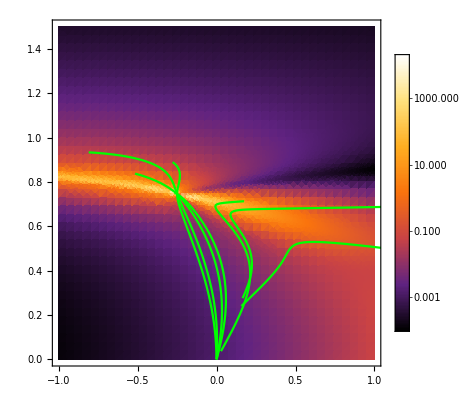

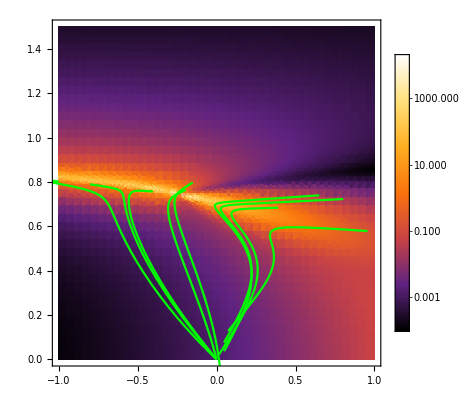

## Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solMulti=Quiet@Table[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{θ,0,π,π/10}];
```

```mathematica
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

-Graphics-

# Direct minimalization

Find geodesics by minimizing the expression for fidelity.

# Singularity and stuff

```mathematica
nn=8;
jj=nn/2; 
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
enSing[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
Manipulate[ContourPlot[enSing[λ,χ]⟦1⟧-enSing[λ,χ]⟦2⟧,{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@densityPlotOptions,Contours->100],
{{λmin,-0.5},-2,2,ImageSize->2000},{{λmax,0},-2,2,ImageSize->2000},{{χmin,0},0,1,ImageSize->2000},{{χmax,1},0,1,ImageSize->2000},ContinuousAction->True]
```

Coordinates of singularities for different nn. For nn = 3 exist only one point {3,-0.5,0.7746}, then at least 2.

```mathematica
sing1={{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73}};
sing2={{4,-0.3,0.8944},{5,-1.5,0.845},{6,-1,0.865},{7,-0.7527,0.7979}};
ListPointPlot3D[sing1,Filling->Bottom]
ListPointPlot3D[sing2,Filling->Bottom]
```

-Graphics3D-

-Graphics3D-

```mathematica
nn=5;
jj=nn/2; 
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
zeroPoints=NSolve[Det[H[λ,χ]]==0,{λ,χ},Reals]
zeroPointsPlot=ListPlot[{λ,χ}/.zeroPoints,PlotRange->All,PlotStyle->Green]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 λ)/87992-(121001 χ)/175984 == 1.

{{λ→-8.14325,χ→10.9678},{λ→-3.93684,χ→4.55109},{λ→-1.70722,χ→1.14989},{λ→0.152014,χ→-1.68629},{λ→-1.31985,χ→0.558981},{λ→-1.26421,χ→0.474103},{λ→-0.360748,χ→-0.904094},{λ→-0.788378,χ→-0.251764},{λ→-0.630875,χ→-0.492028}}

-Graphics-

```mathematica
dens=DensityPlot[Det[gC[l,x]],{l,-10.1,10},{x,-4,4},Evaluate@densityPlotOptions,PlotPoints->20,ScalingFunctions->"Log10"];
Show[dens,zeroPointsPlot]
```

-Graphics-